```mathematica
n=3; (*число клиентов*)
m=n ;(*число коммивояжеров*)
t=Partition[Table[RandomInteger[{1,20}],(n+2)*(n+2)],n+2];(*время,которое требуется, чтобы доехать из i в j*)
Table[t[[i]][[i]]=0,{i,n+2}];
Table[t[[i]][[1]]=0,{i,n+2}];
timewindow=Table[a=RandomInteger[{1,10}];{a, a+RandomInteger[{1, 50}]}, n];(*временные окна*)
a=#[[1]]&/@timewindow;
b=#[[2]]&/@timewindow;
```

```mathematica
V=Range[0,n+1];(*склад, n клиентов,возвращение на склад - вершины графа*)
```

```mathematica
A= Permutations[V,{2}];
A1=DeleteDuplicates[DeleteCases[DeleteCases[DeleteCases[Join[Table[{i,n+1},{i,n}],A],{_,0}],{n+1,_}],{0,n+1}]];(*дуги графа*)
```

```mathematica
lstx=Sort[x[#[[1]],#[[2]]]&/@A1];
varsX=Flatten@Table[Append[lstx[[i]],k],{i,Length@lstx},{k,1,m}];
```

```mathematica
lstu=u[#]&/@V;
varsU=Table[Append[lstu[[i]],k],{i,Length@lstu},{k,1,m}];
```

```mathematica
vars=Join[varsX,Flatten@varsU];
```

```mathematica
objFun=Total[Last@varsU-First@varsU];
c=Last@CoefficientArrays[objFun,vars];
```

```mathematica
con1=Total[Partition[DeleteCases[DeleteCases[varsX,x[0,_,_]],x[n+1,_,_]],{Length[Range[1,n]]*m}],{2}];
rhs1=ConstantArray[{1,0},Length@con1];
```

```mathematica
list2=DeleteCases[DeleteCases[A1,{0,_}],{n+1,_}];
lx=DeleteCases[DeleteCases[varsX,x[0,_,_]],x[n+1,_,_]];

con2=Flatten[Table[Total[Cases[lx,x[list2[[i]][[1]],_,k]]-Cases[varsX,x[_,list2[[i]][[1]],k]]],{i,1,n},{k,m}]];
rhs2=ConstantArray[{0,0},Length@con2];
```

```mathematica
K=10000;
```

```mathematica
con3=Flatten[Cases[Flatten@varsU,u[#[[1]],_]]-Cases[Flatten@varsU,u[#[[2]],_]]+K*Cases[Flatten@varsX,x[#[[1]],#[[2]],_]]&/@A1];
lstt=t[[#[[1]]+1]][[#[[2]]+1]]&/@A1;
rhs3={#,-1}&/@Flatten[ConstantArray[K-#,m]&/@lstt];
```

```mathematica
con4=Flatten[Table[a[[i]]*Total[Cases[Flatten@varsX,x[_,i,k]]]-Cases[Flatten@varsU,u[i,k]],{i,1,n},{k,1,m}]];
rhs4=ConstantArray[{0,-1},Length@con4];
```

```mathematica
con5=Flatten[Table[-b[[i]]*Total[Cases[Flatten@varsX,x[_,i,k]]]+Cases[Flatten@varsU,u[i,k]],{i,1,n},{k,1,m}]];
rhs5=ConstantArray[{0,-1},Length@con5];
```

```mathematica
con6=Flatten[Table[Cases[Flatten@varsU,u[i,k]]-t[[1]][[i+1]]*Cases[varsX,x[0,i,k]],{i,1,n},{k,1,m}]];
rhs6=ConstantArray[{0,1},Length@con6];
```

```mathematica
con7=Flatten@Table[Cases[Flatten@varsU,u[0,k]]-Cases[Flatten@varsU,u[n+1,k]],{k,m}];
rhs7=ConstantArray[{0,-1},Length@con7];
```

```mathematica
con8=Table[Total[Cases[varsX,x[_,n+1,k]]],{k,m}];
rhs8=ConstantArray[{1,-1},Length@con8];
```

```mathematica
lu=Join[ConstantArray[{0,1},Length@varsX],ConstantArray[{0,K},Length@Flatten[varsU]]];
domain=Join[ConstantArray[Integers,Length@varsX],ConstantArray[Reals,Length@Flatten[varsU]]];
matr=Last@CoefficientArrays[Join[con1,con2,con3,con4,con5,con6,con7,con8],vars];
bb=Join[rhs1,rhs2,rhs3,rhs4,rhs5,rhs6,rhs7,rhs8];
```

```mathematica
sol=LinearProgramming[c,matr,bb,lu,domain]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,2.,0.,3.,0.,0.,14.,8.,0.,0.,0.,0.,9.,9.,0.,23.}

{x[0,2,1],x[0,3,3],x[1,4,3],x[2,4,1],x[3,1,3]}

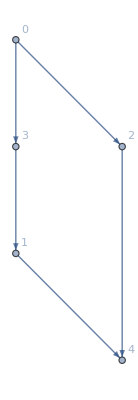

```mathematica
vert=Cases[sol[[;;Length@varsX]]*varsX,Except[0]]
Graph[#[[1]]->#[[2]]&/@vert,VertexLabels->"Name"]
```